```mathematica
alpha[l_,d_, n_]:=l-(d-1)/(2n l);
err[a_]:=CDF[NormalDistribution[0,1],-a];
errextra[l_,d_, n_]:=err[alpha[l,d,n]]-err[l];
N[errextra[5, 10000, 100000]]
```

1.52433×10^-8

```mathematica
Simplify[D[Log[errextra[5 √2, 1000001, Exp[x]]],x]]
Simplify[D[Log[errextra[5 √2, 1000001, x]],x]]
```

((-1+d) ⅇ^(-1/2 (l-(-1+d)/(2 l x))^2))/(l √(2 π) x^2 (Erfc[l/(√2)]-Erfc[(l-(-1+d)/(2 l x))/(√2)]))

(100000 ⅇ^(-25 ⅇ^(-2 x) (-10000+ⅇ^x)^2-x))/(√π (Erfc[5]-Erfc[5-50000 ⅇ^-x]))

(100000 ⅇ^(-(25 (-10000+x)^2)/x^2))/(√π x^2 (Erfc[5]-Erfc[5-50000/x]))

```mathematica
Simplify[D[Log[errextra[l, d, x]],x]]
Simplify[D[Log[errextra[l, d, Exp[x]]],x]]
```

((-1+d) ⅇ^(-1/2 (l-(-1+d)/(2 l x))^2))/(l √(2 π) x^2 (Erfc[l/(√2)]-Erfc[(l-(-1+d)/(2 l x))/(√2)]))

((-1+d) ⅇ^(-1/2 (-((-1+d) ⅇ^-x)/(2 l)+l)^2-x))/(l √(2 π) (Erfc[l/(√2)]-Erfc[(-((-1+d) ⅇ^-x)/(2 l)+l)/(√2)]))

```mathematica
Series[(100000 ⅇ^(-(25 (-10000+x)^2)/x^2))/(√π x (Erfc[5]-Erfc[5-50000/x])),{x,∞,3}]
```

-1-250000/x-57500000000/(3 x^2)+312500000000000/x^3+O[1/x]^4

```mathematica
FullSimplify[Series[((-1+d) ⅇ^(-1/2 (l-(-1+d)/(2 l x))^2))/(l √(2 π) x (Erfc[l/(√2)]-Erfc[(l-(-1+d)/(2 l x))/(√2)])),{x,∞,6}]]
```

-1+(1-d)/(4 x)-((-1+d)^2 (-4+l^2))/(48 l^2 x^2)+(-1+d)^3/(64 l^2 x^3)+((-1+d)^4 (-32+4 l^2+l^4))/(11520 l^4 x^4)-((-1+d)^5 (2+l^2))/(9216 l^4 x^5)-((-1+d)^6 (-128-183 l^2+12 l^4+2 l^6))/(3870720 l^6 x^6)+O[1/x]^7

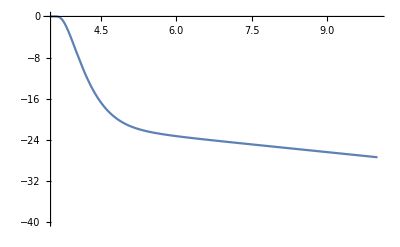

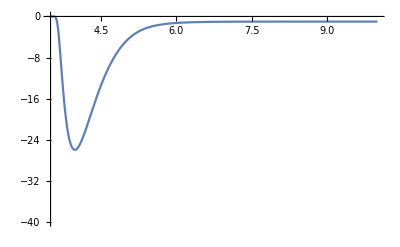

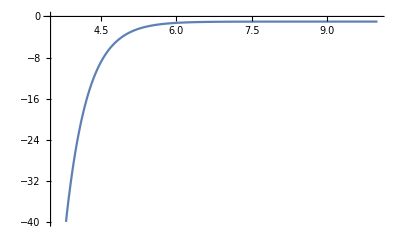

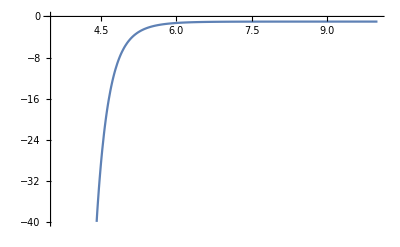

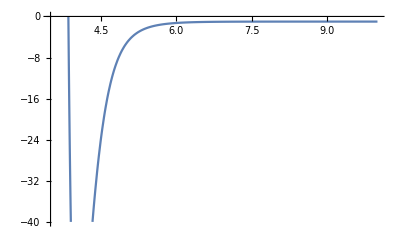

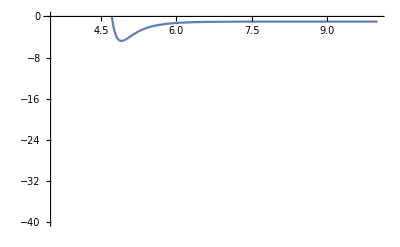

```mathematica
f[x_]:=(2^(9/2-x) 5^(5-x) ⅇ^(-1/2 (10-2^(4-x) 5^(5-x))^2))/(√π (Erfc[5 √2]-Erfc[5 √2 (1-2^(3-x) 5^(4-x))]));
f1[l_,d_,x_]:=-1+(1-d)/(4 x);
f2[l_,d_,x_]:=-1+(1-d)/(4 x)-((-1+d)^2 (-4+l^2))/(48 l^2 x^2);
f3[l_,d_,x_]:=-1+(1-d)/(4 x)-((-1+d)^2 (-4+l^2))/(48 l^2 x^2)+(-1+d)^3/(64 l^2 x^3);
f4[l_,d_,x_]:=-1+(1-d)/(4 x)-((-1+d)^2 (-4+l^2))/(48 l^2 x^2)+(-1+d)^3/(64 l^2 x^3)+((-1+d)^4 (-32+4 l^2+l^4))/(11520 l^4 x^4);
Plot[Log10[errextra[10, 1000001,10^x]],{x,3.5,10},PlotRange->{-40,0}]
Plot[f[x],{x,3.5,10},PlotRange->{-40, 0}]
Plot[f1[10,1000001,10^x],{x,3.5,10},PlotRange->{-40, 0}]
Plot[f2[10,1000001,10^x],{x,3.5,10},PlotRange->{-40, 0}]
Plot[f3[10,1000001,10^x],{x,3.5,10},PlotRange->{-40, 0}]
Plot[f4[10,1000001,10^x],{x,3.5,10},PlotRange->{-40, 0}]
```